```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
DirName=NotebookDirectory[];
```

/Users/qtc325/Trabalhos/NBIA/2024_09_QNMResonantExcitation_ElephantFlea/SphericalSym_ElephFlea_TimeEvol/ExternalCodes

## Frequency Domain

## Load Amplitudes

```mathematica
ao=30;
ϵ=1/10;

spin=2;
l=2;

Nz$QNMload$dom0=200;
Nz$QNMload$dom1=200;

N$QNM$max=17;

Prec=10*MachinePrecision;
```

### Import Data

```mathematica
DirName$InputData="ClusterData/QNM_Amplitudes/eps_"<>ToString[N[ϵ],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm];

fn=DirName$InputData<>"/QNM_Amplitude_Scri_N_"<>ToString[Nz$QNMload$dom0]<>"_nQNM"<>ToString[N$QNM$max+1]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat"


QNM$AmpRaw=Import[fn, "Table"];
QNM$Amp= Delete[QNM$AmpRaw,1];

QNM$AmpSort=SortBy[QNM$Amp, Abs[#[[1]]] &];
```

ClusterData/QNM_Amplitudes/eps_0.1_a0_Over_rh_30./QNM_Amplitude_Scri_N_200_nQNM18_l2_spin2_Prec_159.546.dat

#### Import Schwarzschild for comparision

```mathematica
(*DirName$InputSchwar="ClusterData/QNM_Amplitudes/eps_"<>ToString[N[],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm];

fn=DirName$InputData<>"/QNM_Amplitude_Scri_N_"<>ToString[Nz$QNMload$dom0]<>"_nQNM"<>ToString[N$QNM$max+1]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat"


QNM$AmpRaw=Import[fn, "Table"];
QNM$Amp= Delete[QNM$AmpRaw,1];

QNM$AmpSort=SortBy[QNM$Amp, Abs[#[[1]]] &];*)
```

### Get QNM and Amplitudes

18

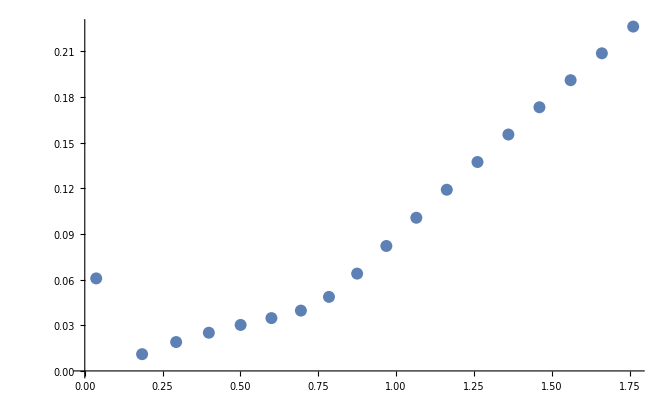

```mathematica
s=QNM$AmpSort[[All,1]]+I*QNM$AmpSort[[All,2]];
A=QNM$AmpSort[[All,3]]+I*QNM$AmpSort[[All,4]];

nQNM=Length@s
sData=Table[ {-QNM$AmpSort[[iqnm,2]],-QNM$AmpSort[[iqnm,1]]}, {iqnm, 1, nQNM}];
ListPlot[sData]
```

## Comparison Against Time Evolution

## Exact QNMs Contributions

```mathematica
hQNM$Scri[τ_, n_]:= 2*Re[ A[[n+1]]*Exp[s[[n+1]]*τ]] (*+ ηϕScri$Conj[[n+1]]*Exp[s$QNM$Conj[[n+1]]*τ];*)



PlotFreqEvol = Table[ LogPlot[Abs@hQNM$Scri[τ,iQNM], {τ,0,100}, WorkingPrecision->100, PlotLabels->{"sQNM_"<>ToString[iQNM]}, PlotStyle->ColorData[iQNM+1,"ColorList"], PlotRange->All], {iQNM, 0,10 }];

Show[PlotFreqEvol]
```

-Graphics-

## Load Time Evolution Data

```mathematica
Print["Load data"];

n$QNM$FirstOrder=0;
WaveDataFile=DirName<>"../data/CteField/spin_"<>ToString[spin]<>"/l_"<>ToString[l]<>"/epsilon_"<>ToString[NumberForm[N[ϵ],{7,6},NumberPadding->{"","0"}]]<>"_a0_"<>ToString[NumberForm[N[ao],{7,6},NumberPadding->{"","0"}]]<>"/N0_5_N1_100_ndom_4_nfields_2/gnuplot2D_field_0_dom_0.dat"
WaveDataRaw1=Import[WaveDataFile, "Table"];

WaveDataHeader1=WaveDataRaw1[[1]]
WaveData1=Delete[WaveDataRaw1,1];
NWave=Length@WaveData1
Time=WaveData1[[All,1]];
h=Time[[2]]-Time[[1]]
hScri=WaveData1[[All,2]];
hHrz=WaveData1[[All,22]];

hQNM$Scri$ExactData=.
hQNM$Scri$ExactData[n_]:=hQNM$Scri[Time,n];
```

Load data

/Users/qtc325/Trabalhos/NBIA/2024_09_QNMResonantExcitation_ElephantFlea/SphericalSym_ElephFlea_TimeEvol/ExternalCodes/../data/CteField/spin_2/l_2/epsilon_0.100000_a0_30.000000/N0_5_N1_100_ndom_4_nfields_2/gnuplot2D_field_0_dom_0.dat

{#1:T,#2:0.000e+00,#3:4.424e-03,#4:7.870e-03,#5:1.055e-02,#6:1.264e-02,#7:1.427e-02,#8:1.554e-02,#9:1.653e-02,#10:1.730e-02,#11:1.790e-02,#12:1.837e-02,#13:1.874e-02,#14:1.902e-02,#15:1.925e-02,#16:1.943e-02,#17:1.957e-02,#18:1.968e-02,#19:1.978e-02,#20:1.986e-02,#21:1.993e-02,#22:2.000e-02}

50001

0.1

#### Map time to index

```mathematica
ti=Time[[1]]
tf=Time[[NWave]]
δt=tf-ti

IndxT[t_]:=Round[(NWave-1)*(t-ti)/δt+1 ];
```

0.

5000.

5000.

## Filtering QNM

Plot data

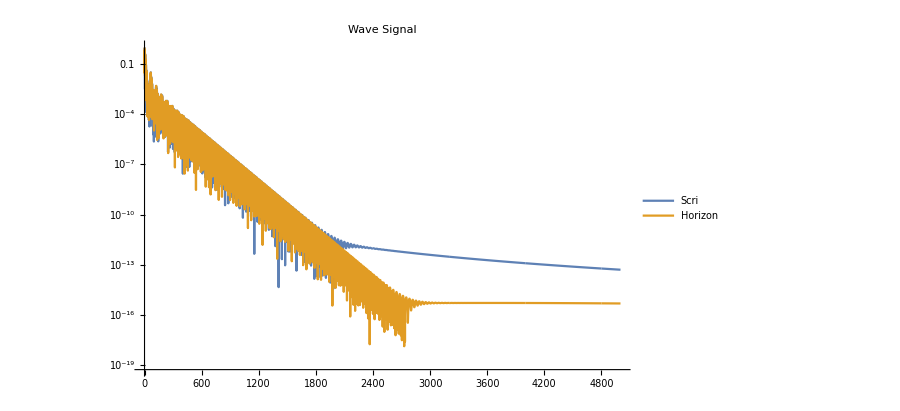

```mathematica
Print["Plot data"];
PlotWave=ListLogPlot[
{Transpose@{Time,Abs@hScri},
Transpose@{Time,Abs@hHrz}
},
PlotLabel->"Wave Signal",
PlotLegends->
{"Scri",
"Horizon"
},
Joined->True
];
Show[PlotWave]
```

### Study Wave

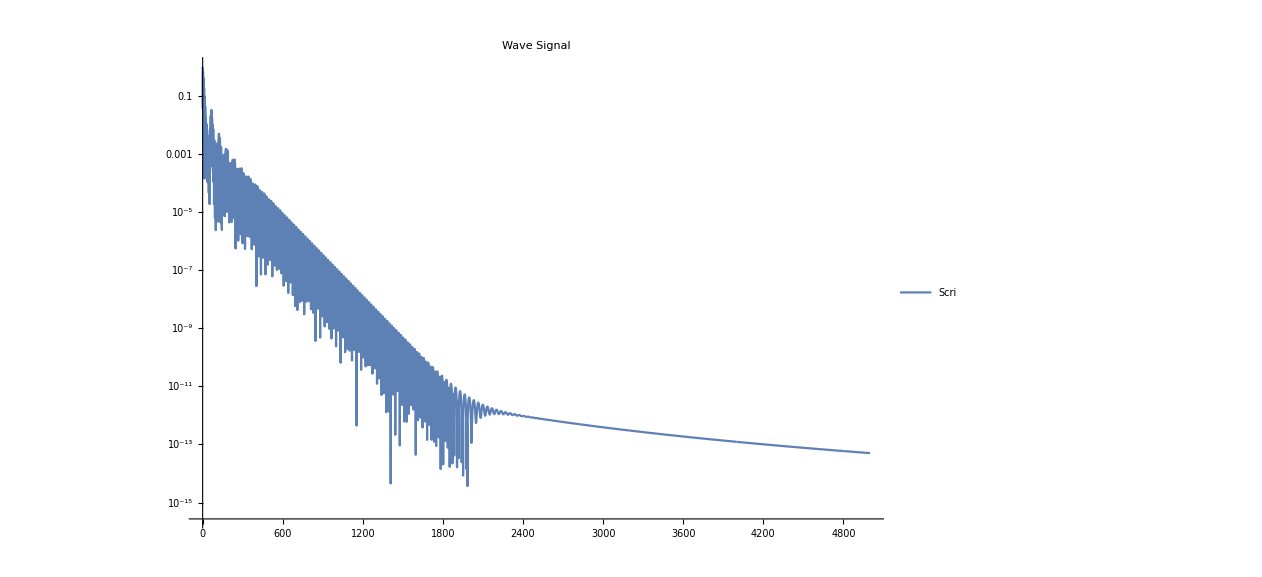

```mathematica
(*WaveBasis=hHrz;
SurfaceName="Horizon";*)

WaveBasis=hScri;
SurfaceName="Scri";

PlotStudy=ListLogPlot[
{Transpose@{Time,Abs@WaveBasis}
},
PlotLabel->"Wave Signal",
PlotLegends->{SurfaceName},
Joined->True
];
Show[PlotStudy]
```

Data Analysis (simple fit as easiest first option): 
(1) Blind test with unknown Amp and unknown ω
(2) Schwarzschild test with unknown Amp, but ω_Schwarz
(3) Elephant Flea test with unknown Amp, but ω_ElFlea

### Filter Fundamental QNM

```mathematica
Wave0=Sum[hQNM$Scri$ExactData[i],{i,0,17}];(*hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5]+hQNM$Scri$ExactData[6]+hQNM$Scri$ExactData[7];*)
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*hQNM$Scri$ExactData[3];*)
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*Wave0=hQNM$Hrz$ExactData;*)

PlotExact=ListLogPlot[
{Transpose@{Time,Abs@WaveBasis},
Transpose@{Time,Abs@Wave0}
},
PlotLabels->{"Full Signal Num", "1stOrder-QNM (n=0) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,100},{10^-10,10}},
ImageSize->Scaled[0.8]
];
Show[PlotExact]
```

-Graphics-

```mathematica
WaveFilter0 = WaveBasis - Wave0;
Wave1=hQNM$Scri$ExactData[0];
(*hQNM$Scri$ExactData[2];*)
(*hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5];*)
(*hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5](*+hQNM$Scri$ExactData[6]*);*)
(*Wave1=hpp$HRz$ExactData*)

PlotFilter0=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter0},
(*Transpose@{Time,Abs@hpm$HRz$ExactData}*)
Transpose@{Time,Abs@Wave1}
},
(*PlotLabels->{"Residual Signal (n=0)" , "2ndOrder-QNM (+-) Exact"},*)
PlotLabels->{"Residual Signal (n=0)" , "1stOrder-QNM (n=1) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,1000},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter0]
```

-Graphics-

### Filter First Overtone

```mathematica
WaveFilter1 =WaveFilter0-Wave1;
Wave2=hQNM$Scri$ExactData[0]+hQNM$Scri$ExactData[1]+hQNM$Scri$ExactData[4]+hQNM$Scri$ExactData[5];
(*Wave2=hpm$HRz$ExactData;*)

PlotFilter1=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter1}(*,*)
(*Transpose@{Time,Abs@Wave2}*)
},
(*PlotLabels->{"Residual Signal (n=0, +-)" , "2ndOrder-QNM (++) Exact"},*)
PlotLabels->{"Residual Signal (n=0, n=1)" , "1stOrder-QNM (n=2) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,40},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter1]
```

-Graphics-

### Filter Second Overtone

```mathematica
WaveFilter2 =WaveFilter1 - Wave2;
(*Wave3=hQNM$Scri$ExactData[3];*)
PlotFilter2=ListLogPlot[
{Transpose@{Time,Abs@WaveFilter2}(*,
Transpose@{Time,Abs@Wave3}*)
},
PlotLabels->{"Residual Signal (n=0, n=1, n=2)", "1stOrder-QNM (n=3) Exact"},
PlotLegends->SurfaceName,
Joined->True,
PlotRange->{{0,30},{10^-10,1}},
ImageSize->Scaled[0.8]
];
Show[PlotFilter2]
```

-Graphics-

```mathematica
hFIT=A*exp(s0*t)+B*exp(s1*t)
```

A exp s0 t+B exp s1 t

(i) We known s0 and s1 from freq. domain. Fit for A and B. Do we recover prediction from ID? Guess: Yes
(ii) Blind agnostic test: fit for (A,B, s0, s1). Do we recover the avoid crossing QNMs? Guess: No ?

## “Fourier” Analysis Time Domain Signal - Poor Man Data Analysis

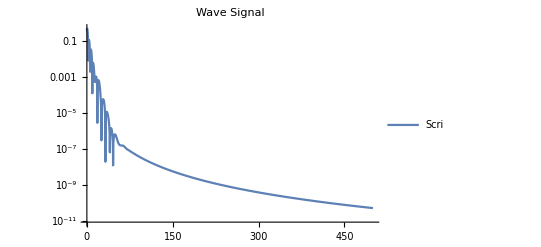

```mathematica
WaveStudy=WaveBasis-(hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3]);
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)(*WaveBasis;*)
(*hQNM$Scri$ExactData[2]+hQNM$Scri$ExactData[3];*)
(*WaveBasis;*)

PlotTimeSignal=ListLogPlot[
{Transpose@{Time,Abs@WaveStudy}
},
PlotLabel->"Wave Signal",
PlotLegends->
{"Scri"},
Joined->True,
ImageSize->Scaled[0.8]
];
Show[PlotTimeSignal]
```

### Select QNM phase

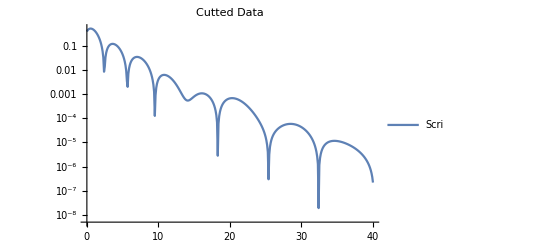

```mathematica
t0=0;I0=IndxT[t0];
t1=40; I1=IndxT[t1];
tData=Table[ Time[[i]],{i,I0,I1}];
Data=Table[WaveStudy[[i]],{i,I0,I1}];

NData=Length@Data;
PlotData=ListLogPlot[
{Transpose@{tData,Abs@Data}
},
PlotLabel->"Cutted Data",
PlotLegends->
{"Scri"},
Joined->True
];
Show[PlotData]
```

```mathematica
Data2Fit=Transpose@{tData,Data};

nQNM$Fit=3;

model=Sum [ A[i]*Exp[-ωi[i] *t]Sin[ϕ[i]+ωr[i]*t] ,{i,1,nQNM$Fit}]
modelpar=Table[{A[i],ϕ[i],ωi[i], ωr[i]},{i,1,nQNM$Fit}]//Flatten
nlm=NonlinearModelFit[Data2Fit,model,modelpar,t, MaxIterations->Infinity, AccuracyGoal->0.5*MachinePrecision, PrecisionGoal->0.5*MachinePrecision,  WorkingPrecision->MachinePrecision]//Normal
nlm$data=nlm/.t->tData;
Residual=Abs[Data-nlm$data]/Abs[Data];

FittedData=Transpose@{tData,nlm$data};
ResidualData=Transpose@{tData,Residual};

ListLogPlot[{Abs@Data2Fit,Abs@FittedData}, Joined->True, PlotLabels->{"Data", "Fit"}]
ListLogPlot[Abs@ResidualData, Joined->True, PlotLabels->{"Residual"}]

N@s$QNM[[3]]
N@s$QNM[[4]]
```

ⅇ^(-t ωi[1]) A[1] Sin[ϕ[1]+t ωr[1]]+ⅇ^(-t ωi[2]) A[2] Sin[ϕ[2]+t ωr[2]]+ⅇ^(-t ωi[3]) A[3] Sin[ϕ[3]+t ωr[3]]

{A[1],ϕ[1],ωi[1],ωr[1],A[2],ϕ[2],ωi[2],ωr[2],A[3],ϕ[3],ωi[3],ωr[3]}

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (MachinePrecision).

0.370677 ⅇ^(-0.925296 t) Sin[3.26932-1.06317 t]+0.536032 ⅇ^(-0.414844 t) Sin[2.14202-0.910955 t]-0.0262829 ⅇ^(-0.181904 t) Sin[7.76595+0.445763 t]

-Graphics-

-Graphics-

-0.217235-0.736313 ⅈ

-0.211645+0.739198 ⅈ

```mathematica
sSchwarzschil$n0=-0.1779246313778724125652120005152178509675423181561187703639623721770992017316962715759234642097336789737598225764160641944325887735662226216980430348181479+I* 0.747343368836081044564012120434754107823160172903535881938910623355711335675523008900239525461539174202261286644053489464729872338914566586615874614796782;
N[sSchwarzschil$n0,3]
```

-0.18+0.747 ⅈ

```mathematica
N@s$QNM
```

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ}

### Fourier Analysis

#### Poor-man Routine to read local maximum

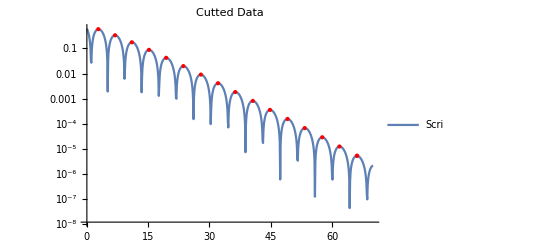

```mathematica
kmax=1;
kk=1;
MaxPos={};
While[kk<NData,
For[k=kmax+1, k<NData, k++,
Fm1=Abs@Data[[k-1]];
F=Abs@Data[[k]];
Fp1=Abs@Data[[k+1]];

If[F>Fm1 && F>Fp1,
kmaxt=k;
Break[];
];
];
kmax=kmaxt;
MaxPos=Append[MaxPos,kmax];
kk=k;
]
MaxSize=Length@MaxPos;
MaxData=Table[{tData[[MaxPos[[n]]]],Abs@Data[[MaxPos[[n]]  ]]}, {n,1,MaxSize}];
PlotMax=ListLogPlot[MaxData, PlotRange->Full, PlotStyle->{Red,PointSize[Medium]}];
Show[PlotData,PlotMax]
```

#### Fit Exponential

-0.18690669828540074

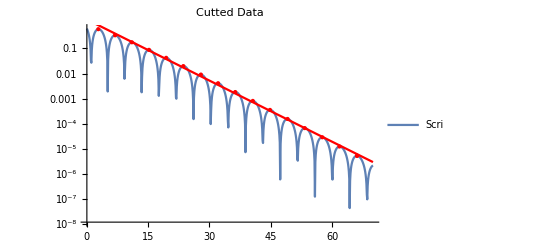

```mathematica
FitData=Table[{MaxData[[i,1]],Log@MaxData[[i,2]]},{i,1,MaxSize}];
FitExp=Fit[FitData,{1,t},t];
PlotFit=LogPlot[Exp@FitExp, {t,t0,t1}, PlotStyle->Red];
ωI=D[FitExp,t]
Show[PlotData,PlotMax, PlotFit]
```

#### Fourier Transform According to Help

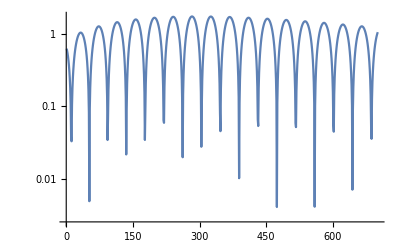

```mathematica
Period=Table[ Data[[k]]*Exp[-ωI*tData[[k]]], {k,1, NData}];
PlotPeriod=ListLogPlot[Abs@Period, PlotRange->Full, Joined->True];
Show[PlotPeriod]
```

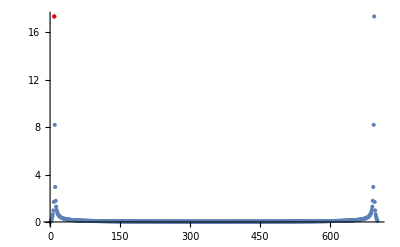

```mathematica
FourierPeriod=Abs[Fourier[Period]];

NFourier=Length@FourierPeriod;
FourierPeriod1=Table[FourierPeriod[[i]], {i,1,NFourier/2}];
FourierPeriod2=Table[FourierPeriod[[i-NFourier/2]], {i,NFourier/2+1,NFourier}];
pos = Position[FourierPeriod1, Max[FourierPeriod1]][[1,1]];


Show[ListPlot[FourierPeriod], Graphics[{Red, Point[{pos, FourierPeriod[[pos]]}]}], PlotRange->All]
```

```mathematica
fr = Abs[Fourier[Period Exp[2 Pi I (pos - 2) N[Range[0, NData - 1]]/NData], FourierParameters->{0,2/NData}]];
frpos = Position[fr, Max[fr]][[1,1]]
```

451

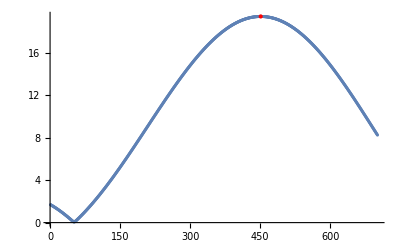

```mathematica
Show[ListPlot[fr], Graphics[{Red, Point[{frpos, fr[[frpos]]}]}], PlotRange->All]
```

```mathematica
Per=N[NData/(pos - 2 + 2 (frpos - 1)/NData)];
ωR=N[2*Pi/(Per*h)]
```

0.742499

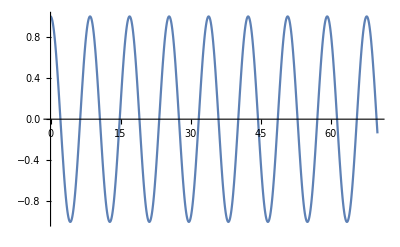

```mathematica
Plot[Cos[ωR*t], {t,t0,t1}]
```

#### Print Results

```mathematica
Print["Imaginary QNM ωI = ",ωI]
Print["Real QNM ωR  = ",ωR]
```

Imaginary QNM ωI = -0.18690669828540074

Real QNM ωR  = 0.742499

```mathematica
N[s$QNM]
```

{-0.304656-0.162407 ⅈ,-0.251156-0.433143 ⅈ,-0.217235-0.736313 ⅈ,-0.211645+0.739198 ⅈ,-0.36968+0.971584 ⅈ,-0.480186-1.18411 ⅈ}

```mathematica
s$mean=(N[s$QNM[[3]]]+Conjugate[N[s$QNM[[4]]]])/2
```

-0.21444-0.737755 ⅈ

```mathematica
sSchwarzschil$n0=-0.1779246313778724125652120005152178509675423181561187703639623721770992017316962715759234642097336789737598225764160641944325887735662226216980430348181479+I* 0.747343368836081044564012120434754107823160172903535881938910623355711335675523008900239525461539174202261286644053489464729872338914566586615874614796782;
N[sSchwarzschil$n0,3]
```

-0.18+0.747 ⅈ